# One wave

## Play

```mathematica
Clear["Global`*"]
```

```mathematica
ν=400;
```

```mathematica
f[t_]=Sin[2π ν t]
```

Sin[800 π t]

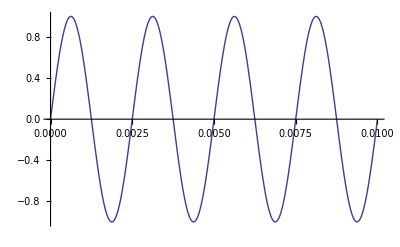

```mathematica
Plot[f[t],{t,0,0.01}]
```

```mathematica
play=Play[f[t],{t,0,3}]
```

-Graphics-

## Export

### Get current notebook directory

```mathematica
CurrentNotebookDirectory=NotebookDirectory[SelectedNotebook[]]
```

/Users/Soha/Google Drive/Café Planck/Physics/03-Sound waves/

### Set Directory to current notebook directory

```mathematica
SetDirectory[CurrentNotebookDirectory]
```

/Users/Soha/Google Drive/Café Planck/Physics/03-Sound waves

### Get current notebook name

```mathematica
CurrentNotebookName=StringTake[ToString[SelectedNotebook[]],{18,StringPosition[ToString[SelectedNotebook[]],">",1][[1,1]]-1}]
```

02-One wave.nb

### Export

```mathematica
fileName=StringJoin[StringDrop[CurrentNotebookName,-3],".wav"];
```

```mathematica
Export[fileName,play];
```